# Vaje iz Mathematice, 1. del

### 1. naloga:

Izračunaj vrednost izraza  ((20+316)^7-55)/(33·12)^3

```mathematica
izraz1  =((20+316)^7 - 55)/(33*12)^3
```

```mathematica
483476023799709641/62099136
```

Izračunaj še numerično vrednost istega izraza na 20 mest natančno.

```mathematica
N[izraz1, 20]
```

7.7855515381036805568×10^9

### 2. naloga:

Poenostavi izraz  2^x+5a 2^x+2^(x+2)

```mathematica
izraz2=2^x+5a 2^x+2^(x+2)
```

2^x+2^(2+x)+5 2^x a

```mathematica
Simplify[izraz2]
```

5 2^x (1+a)

### 3. naloga:

Poišči največji skupni delitelj števil 536, 1248, 2320.

```mathematica
GCD[536,1248,2320]
```

8

Poišči še najmanjši skupni večkrat teh števil.

```mathematica
LCM[536,1248,2320]
```

12124320

### 4. naloga:

Seštej vsa soda števila na intervalu [1,100].

```mathematica
Sum[2i,{i,1,50}]
```

2550

```mathematica
Sum[i,{i,2,100,2}]
```

2550

### 5. naloga:

Izračunaj  ∑_(k=1)^∞ (k^2+1)/k^4

```mathematica
Sum[(k^2+1)/k^4,{k,1,Infinity}]
```

1/90 π^2 (15+π^2)

### 6. naloga:

Izračunaj vrednost izraza (sin α + sin β)/(cos^2(α - β) - sin^2(β-α)) za kota α=1830°  in  β=270°.

```mathematica
izraz6=(Sin[a]+Sin[b])/(Cos[a-b]^2-Sin[b-a]^2)
```

(Sin[a]+Sin[b])/(Cos[a-b]^2-Sin[a-b]^2)

```mathematica
izraz6 /. {a -> 1830 Degree, b-> 270 Degree}
```

1

### 7. naloga:

Izračunaj vrednost izraza  (x^5-2 x^2+3x+4)/(x^5-2x-1)  pri x=1, 2, ..., 10. 
Uporabi transformacijsko pravilo in ukaz  ReplaceAll  oz.  /.

```mathematica
izraz7=(x^5-2x^2+3x+4)/(x^5-2x-1)
izraz7 /. x-> {1,2,3,4,5,6,7,8,9,10}
izraz7 /. x-> Range[10]
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

izraz7

Isto nalogo reši še s pomočjo ukaza Table.

```mathematica
Table[izraz7,{x,1,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

### 8. naloga:

Dan je pravilen šestkotnik s stranico r. Kolikšna je ploščina kolobarja, ki ga določata včrtana in očrtana krožnica?

```mathematica
Simplify[r^2*Pi-(r*Sqrt[3]/2)^2*Pi]
```

(π r^2)/4

### 9. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih?

```mathematica
Solve[{s== h+3,m==23+s,m-6== (s-6+h-6)+4}]
```

{{h→25,m→51,s→28}}

### 10. naloga:

Poišči vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2

```mathematica
Solve[Conjugate[z]==z^2]
```

{{z→0},{z→1},{z→-1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

### 11. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36?

```mathematica
Solve[Sum[16-2n,{1,n}]==36/. n]
```

Sum::itraw: Raw object 1 cannot be used as an iterator.

Sum::vloc: The variable 1 cannot be localized so that it can be assigned to numerical values.

ReplaceAll::reps: {n} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::naqs: ∑_1^n (16-2 n)==36/.n is not a quantified system of equations and inequalities.

Solve[∑_1^n (16-2 n)==36/.n]

### 12. naloga:

Dokaži, da je x=1 rešitev enačbe  a x^2-2b x+c=0, če a, b in c sestavljajo aritmetično zaporedje.

```mathematica
Solve[a*x^2-2b*x+c== 0/. {b->a+k,c->a+2k},x]
```

{{x→1},{x→(a+2 k)/a}}

### 13. naloga:

Določi vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a + 5x), da bo  x=2  rešitev enačbe.

```mathematica
Solve[(2a*x+3a)/(3a+5x)== ( 3a-4)/(3a+5x)/. {x->2},a]
```

{{a→-1}}

### 14. naloga:

Na kakšne načine lahko plačamo poštnino 2,27 EUR z znamkami za 10, 23 in 37 centov?

```mathematica
Solve[{x*10+y*23+z*37== 227, x≥ 0, y≥ 0,z≥ 0},Integers]
```

{{x→1,y→3,z→4},{x→2,y→9,z→0},{x→7,y→2,z→3},{x→13,y→1,z→2},{x→19,y→0,z→1}}

### 15. naloga:

Poišči štirimestno število, ki je popoln kvadrat in katerega prvi dve števki sta med seboj enaki, drugi dve pa prav tako med seboj enaki.

```mathematica
Solve[{1100x+11y==n^2,x>0,y≥0,x≤9,y≤9,n≥0},Integers]
```

{{n→88,x→7,y→4}}

### 16. naloga:

Na kocko s stranico a postavimo drugo kocko s telesno diagonalo, enako stranici prve kocke, na drugo kocko spet tretjo s telesno diagonalo, enako stranici druge kocke, in to ponavljamo brez konca. Izračunaj višino tako dobljenega telesa.

```mathematica
FullSimplify[Sum[a/Sqrt[3]^n,{n,0,Infinity}]]
```

1/2 (3+√3) a

Izračunaj še prostornino tako dobljenega telesa.

```mathematica
FullSimplify[Sum[a/Sqrt[3]^n]^3,{n,0,Infinity}]
```

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

FullSimplify::bass: 0 is not a well-formed assumption.

Sum[a/(√3)^n]^3

### 17. naloga:

Določi premico y=k x+n, ki gre skozi točki (-2,3) in (6,-1).

```mathematica
premica=y==kx+n
```

y==kx+n

```mathematica
Solve[{premica/.{x->-2,y->3},premica/.{x->-1,y->6}}]
```

Nariši dobljeno premico na intervalu [-3,7] tako, da bosta enoti na koordinatnih oseh enako veliki.
Na sliki označi še točki, skozi kateri poteka premica.

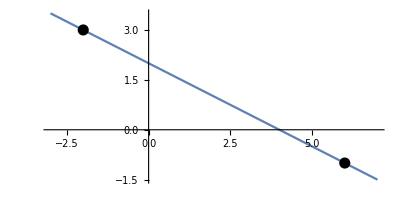

```mathematica
Plot[-x/2+2,{x,-3,7},AspectRatio->Automatic,Epilog->{PointSize[0.02],Point[{{-2,3},{6,-1}}]}]
```

### 18. naloga:

```mathematica
Clear[x]
```

```mathematica
Clear[y]
```

Določi inverzno funkcijo funkcije  y=2ln(3x-1)

```mathematica
Solve[y==2 * Log[1-3 x]/.{x->y,x-> y},y,Reals]
```

{{y→0}}

Nariši grafa obeh funkcij v istem koordinatnem sistemu.

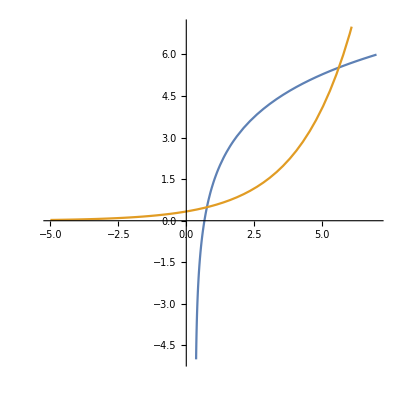

```mathematica
Plot[{2Log[3x-1],1/3*(Exp[x/2])},{x,-5,7},AspectRatio->Automatic,PlotRange->{-5,7}]
```